```mathematica
file="/Users/WillC/Documents/Rutgers/Research/RADICAL/Cloud-Master/data/output/Comet_test_001/weak_scale_output/data.csv";
rawdata= Import[file];
header = rawdata[[1]]
data = rawdata[[2;;,2;;]]
```

{Test Directory,2 ^ Number of Cores,2 ^ Jobs per Cores,Run Time}

{{1.,1.,4.33969},{1.,2.,7.74974},{1.,4.,14.5627},{1.,8.,27.7742},{1.,16.,58.1951},{1.,32.,112.432},{1.,64.,215.876},{1.,128.,434.515},{1.,256.,869.557},{1.,512.,1752.21},{1.,1024.,3455.97},{2.,1.,4.44316},{2.,2.,7.95156},{2.,4.,14.9646},{2.,8.,28.957},{2.,16.,55.5302},{2.,32.,110.922},{2.,64.,222.686},{2.,128.,448.382},{2.,256.,888.026},{2.,512.,1762.11},{2.,1024.,3563.47},{4.,1.,4.45789},{4.,2.,7.84757},{4.,4.,14.6606},{4.,8.,28.5913},{4.,16.,55.9236},{4.,32.,112.149},{4.,64.,222.338},{4.,128.,444.499},{4.,256.,890.885},{4.,512.,1792.68},{4.,1024.,3539.92},{8.,1.,4.6626},{8.,2.,7.76086},{8.,4.,14.5537},{8.,8.,28.4721},{8.,16.,55.9422},{8.,32.,112.442},{8.,64.,225.134},{8.,128.,446.209},{8.,256.,894.709},{8.,512.,1780.68},{8.,1024.,3533.01},{16.,1.,4.35932},{16.,2.,7.85255},{16.,4.,14.7718},{16.,8.,28.4203},{16.,16.,57.0813},{16.,32.,111.881},{16.,64.,224.055},{16.,128.,446.641},{16.,256.,877.542},{16.,512.,1768.34},{16.,1024.,3589.41}}

4

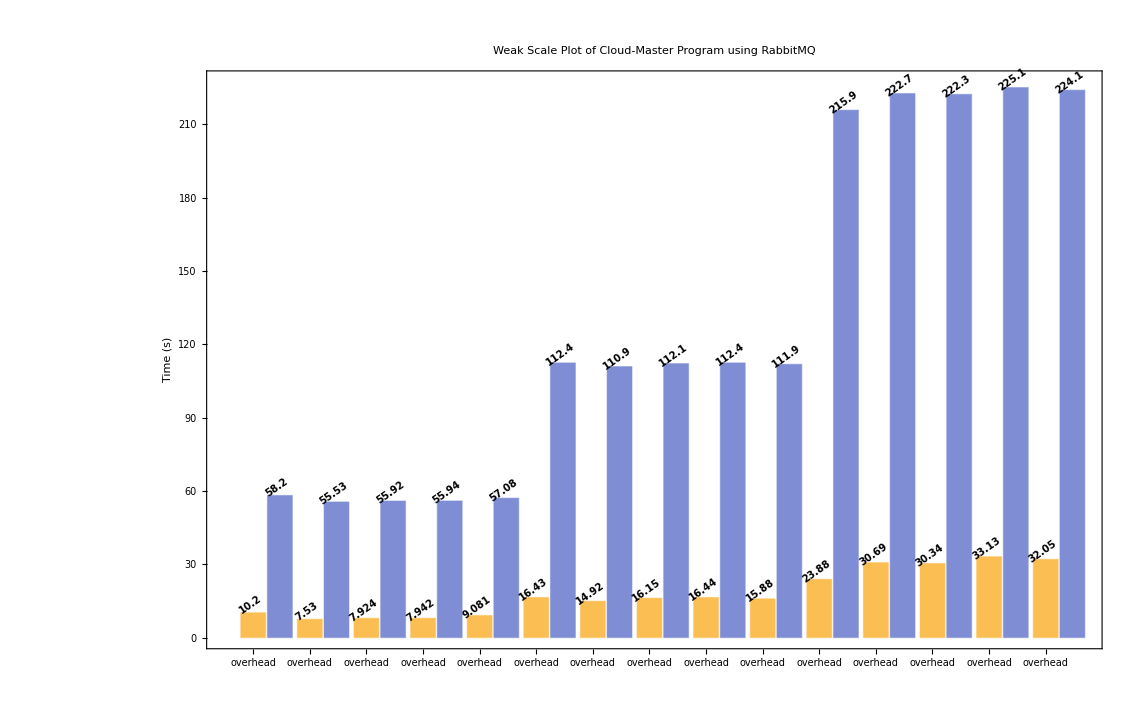

```mathematica
weakScale=Table[data[[testsPerNumCores*x+y]],{y,1,11},{x,0,4}];
weakScaleCores=Table[
ToString[IntegerPart[weakScale[[x]][[y]][[2]]]]<>" Jobs/Core\n"<>ToString[IntegerPart[weakScale[[x]][[y]][[1]]]]<>" Cores"
,{x,1,Length[weakScale]}
,{y,1,Length[weakScale[[1]]]}];
weakScaleJobsPerCore=Table[ToString[IntegerPart[weakScale[[x]][[y]][[2]]]]<>" Jobs/Core",{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleExpected=Table[sleepTime*weakScale[[x]][[y]][[2]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleExperimental=Table[weakScale[[x]][[y]][[3]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];
weakScaleOverHead=Table[weakScaleExperimental[[x]][[y]]-weakScaleExpected[[x]][[y]],{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];

precision=4
weakScaleCompare=Table[{SetPrecision[weakScaleOverHead[[x]][[y]],precision],SetPrecision[weakScaleExperimental[[x]][[y]],precision]},{x,1,Length[weakScale]},{y,1,Length[weakScale[[1]]]}];

chartRange={5,7};
BarChart[
Flatten[weakScaleCompare[[chartRange[[1]];;chartRange[[2]]]],1],
ChartLabels->{
Placed[Flatten[weakScaleCores,1],Axis],
Placed[{"overhead","total"},Axis]
},
LabelingFunction->(Placed[Rotate[Style[#1,10,Bold],35 Degree],Above]&),
Frame->True,
FrameLabel->{"",Style["Time (s)",15]},
PlotLabel->Style["Weak Scale Plot of \nCloud-Master Program using RabbitMQ",20,Bold],
PlotRange->{All,{0,Max[weakScaleCompare[[chartRange[[1]];;chartRange[[2]]]]]+Max[weakScaleCompare[[chartRange[[1]];;chartRange[[2]]]]]*.01}}
]
```

#### Comet Weak Scale Plot

Using RabbitMQ

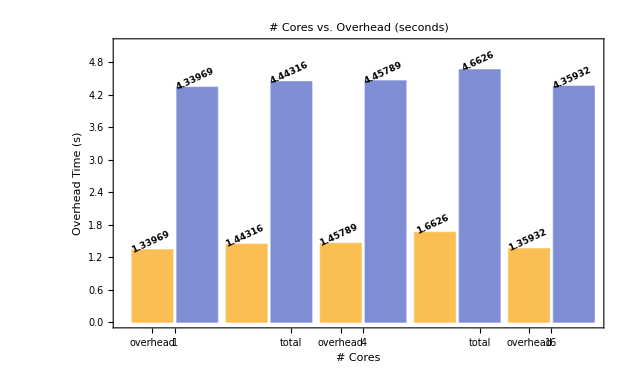

```mathematica
sleepTime=3;
testsPerNumCores = 11;
weakScale=Table[data[[testsPerNumCores*x+y]],{y,1,11},{x,0,4}][[1]];
weakScaleCores=Table[IntegerPart[weakScale[[x]][[1]]],{x,1,Length[weakScale]}];
weakScaleExpected=Table[sleepTime*weakScale[[x]][[2]],{x,1,Length[weakScale]}];
weakScaleExperimental=Table[weakScale[[x]][[3]],{x,1,Length[weakScale]}];
weakScaleOverHead=Table[weakScaleExperimental[[x]]-weakScaleExpected[[x]],{x,1,Length[weakScale]}];

weakScaleCompare=Table[{weakScaleOverHead[[x]],weakScaleExperimental[[x]]},{x,1,Length[weakScale]}];

BarChart[
weakScaleCompare,
ChartLabels->{Placed[weakScaleCores,Axis],Placed[{"overhead","total"},Axis]},
LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),
Frame->True,
FrameLabel->{"# Cores","Overhead Time (s)"},
PlotLabel->"# Cores vs. Overhead (seconds)",
PlotRange->{All,{0,Max[weakScaleCompare]+Max[weakScaleCompare]*.1}}
]
```

#### ILAB 8-Core Test Plot

```mathematica
sleepseconds=300;
ilabtime=Table[{sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]],rawdata[[x]][[1]][[3]]},{x,1,Length[rawdata]}];
ilabjob=Table[rawdata[[x]][[1]][[2]],{x,1,Length[rawdata]}];
ilabjobString=Table[ToString[rawdata[[x]][[1]][[2]]],{x,1,Length[rawdata]}];
ilaboverhead=Table[Abs[sleeptime*rawdata[[x]][[1]][[2]]/rawdata[[x]][[1]][[1]]-rawdata[[x]][[1]][[3]]],{x,1,Length[rawdata]}];
```

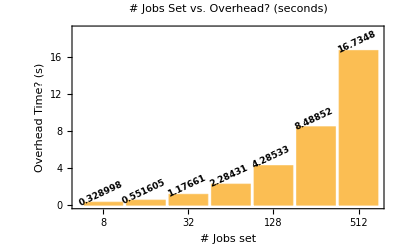

```mathematica
overhead = BarChart[ilaboverhead,ChartLabels->ilabjobString,LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Overhead Time? (s)"},PlotLabel->"# Jobs Set vs. Overhead? (seconds)",PlotRange->{All,{0,19}}]
```

```mathematica
sidebyside=BarChart[ilabtime,ChartLabels->{ilabjobString,{"expected","meas."}},LabelingFunction->(Placed[Rotate[Style[#1,9,Bold],25 Degree],Above]&),Frame->True,FrameLabel->{"# Jobs set","Time (s)"},PlotLabel->"# Jobs Set vs. Time (seconds)",PlotRange->{All,{0,20500}}]
```

```mathematica
Roverhead=Rasterize[overhead,ImageResolution->200]
Rsidebyside=Rasterize[sidebyside,ImageResolution->500]
```

#### Linear Fit

```mathematica
lm = LinearModelFit[avgPoints,x,x];
Normal[lm]
```

```mathematica
Normal[lm]
```

86.0805-10.4321 x

```mathematica
standardError[ts_]:=StandardDeviation[ts]/Abs[ts]
```

```mathematica
stderr=standardError[avgPoints[[All,2]]]
stderr=Table[{avgPoints[[i,1]],avgPoints[[i,2]],stderr[[i]]},{i,1,3}]
```

{0.211747,0.242451,0.360908}

{{1,75.2895,0.211747},{2,65.7549,0.242451},{4,44.1728,0.360908}}

```mathematica
points=ListPlot[avgPoints,PlotRange->{{0,5},All},PlotMarkers->{Automatic,Small},PlotStyle->{Black,Opacity[0.5]}];

fit=Plot[lm[x],{x,0,5},PlotStyle->{Gray,Dashed},PlotLegends->{"Linear Fit\n"<>ToString[Normal[lm]], FontSize->12}];

Needs["ErrorBarPlots`"]
errplot=ErrorListPlot[stderr,PlotMarkers->{".",Tiny},PlotStyle->{Blue}];

final=Show[{fit,errplot(*,points*)},Frame->True,FrameLabel->{"# cores set","Time (s)"},LabelStyle->Bold,PlotLabel->"# Cores vs. Average MonteCarlo Runtimes",PlotRange->{All,{40,80}}]
```